## Trapping/Cooling Grid Searches

```mathematica
SetDirectory@NotebookDirectory[]
h="5.00";
analysisResults=Import["wellNumericParams(eta_"<>h<>").csv"];
```

C:\Users\ruvil\OneDrive\Ruvi\Schoolwork\ANU\PhD\Projects\Levitating Mirror\Papers\PTStabilisationPaper\Code\fig5_TrappingCooling

### Cooling Widths

```mathematica
n=-1;
trappingCoolingParams=Take[#,3]&/@analysisResults[[1;;n]];
coolingWidths=#[[4]]&/@analysisResults[[1;;n]];
```

```mathematica
(* https://mathematica.stackexchange.com/a/20029/7893 *)
minCooling=Min@coolingWidths;
maxCooling=Max@coolingWidths;
colours=ColorData["BlueGreenYellow"][(#-minCooling)/(maxCooling-minCooling)]&/@coolingWidths;
```

```mathematica
labelStyle=Directive[FontSize->30,FontColor->Black,FontFamily->"Times New Roman"];
plotOpts=Sequence[ImageSize->Large,LabelStyle->labelStyle];
```

```mathematica
tcPlot=Row@{Graphics3D[Point[trappingCoolingParams,VertexColors->colours],plotOpts,Axes->True,BoxRatios->{1,1,1/GoldenRatio},AxesLabel->{"g̃","B̃","(Δ̃)_βα"},ViewPoint->{-3.066102374488156,-1.2494612815820678,0.6984717138047823},ViewVertical->{-0.24704645037040798,-0.1066369957942482,0.9631181664195517}],BarLegend[{"BlueGreenYellow",{minCooling,maxCooling}},LegendMarkerSize->400,LegendLabel->"Width (ℓ)",LabelStyle->labelStyle]};
Rasterize[tcPlot]
```

-Graphics-

```mathematica
Export["figTrappingCooling_Widths_h"<>h<>".png",Rasterize[tcPlot,ImageResolution->300]];
```

### Cooling Depths

```mathematica
coolingDepths=#[[6]]&/@analysisResults[[1;;n]];
minCoolingDepths=Min@coolingDepths;
maxCoolingDepths=Max@coolingDepths;
```

```mathematica
coloursDepths=ColorData["SunsetColors"][(#-minCoolingDepths)/(maxCoolingDepths-minCoolingDepths)]&/@coolingDepths;
tcDepthsPlot=Row@{Graphics3D[Point[trappingCoolingParams,VertexColors->coloursDepths],plotOpts,Axes->True,BoxRatios->{1,1,1/GoldenRatio},AxesLabel->{"g̃","B̃","(Δ̃)_βα"},ViewPoint->{-3.066102374488156,-1.2494612815820678,0.6984717138047823},ViewVertical->{-0.24704645037040798,-0.1066369957942482,0.9631181664195517}],BarLegend[{"SunsetColors",{0,maxCoolingDepths}},LegendMarkerSize->400,LegendLabel->"Depth (mℓ^2ν^2)",LabelStyle->labelStyle]};
Rasterize[tcDepthsPlot]
```

-Graphics-

```mathematica
Export["figTrappingCooling_Depths_h"<>h<>".png",Rasterize[tcDepthsPlot,ImageResolution->300]];
```

### Cooling Areas

```mathematica
coolingAreas=Max[#,0]&/@(coolingWidths*coolingDepths);
minCoolingAreas=Min@coolingAreas;
maxCoolingAreas=Max@coolingAreas;

(*colorsAndOpacities=MapThread[Darker[ColorData["SunsetColors"][(#1-minCooling)/(maxCooling-minCooling)],1-(#2-minCoolingAreas)/(maxCoolingAreas-minCoolingAreas)]&,{coolingWidths,coolingAreas}];*)
```

```mathematica
colorsAreas=ColorData["SunsetColors"][(#1-minCoolingAreas)/(maxCoolingAreas-minCoolingAreas)]&/@coolingAreas;
fullPlot=Row@{Graphics3D[Point[trappingCoolingParams,VertexColors->colorsAreas],plotOpts,Axes->True,BoxRatios->{1,1,1/GoldenRatio},AxesLabel->{"g̃","B̃","(Δ̃)_βα"},ViewPoint->{-3.066102374488156,-1.2494612815820678,0.6984717138047823},ViewVertical->{-0.24704645037040798,-0.1066369957942482,0.9631181664195517}],BarLegend[{"SunsetColors",{minCoolingAreas,maxCoolingAreas}},LegendMarkerSize->400,LegendLabel->"Area (mℓ^3ν^2)",LabelStyle->labelStyle]};
Rasterize[fullPlot]
```

-Graphics-

```mathematica
Export["figTrappingCooling_Areas_h"<>h<>".png",Rasterize[fullPlot,ImageResolution->300]];
```

## Visualising the well

```mathematica
TwoLaserPotential[x_,g_:g0,B_:B0,Δ_:Δ0]:=g x-ArcTan[x]-B^2 ArcTan[x+Δ]
TwoLaserHeating[x_,g_:g0,B_:B0,Δ_:Δ0]:=(4x)/((1+x^2)^3)+B^2(4(x+Δ))/((1+(x+Δ)^2)^3)

pos=First@Flatten@Position[coolingAreas,maxCoolingAreas];
(*pos=First@Flatten@Position[coolingDepths,maxCoolingDepths];*)
width=coolingWidths[[pos]]
depth=coolingDepths[[pos]]
paramsToVis=trappingCoolingParams[[pos]]
x0=analysisResults[[pos]][[5]]
```

1.25112511251125191

0.0270807896522426983

{0.36873747494989978,0.470941883767535041,-2.63263263263263259}

1.77517751775177501

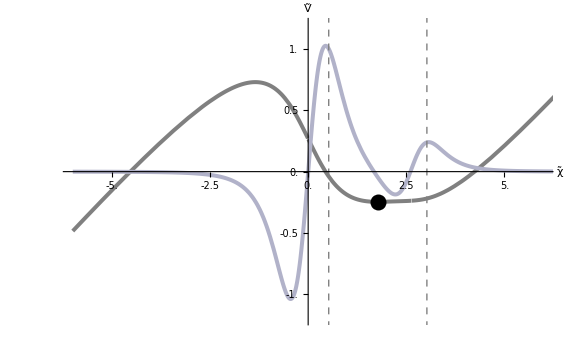

```mathematica
g0=paramsToVis[[1]];B0=paramsToVis[[2]];Δ0=paramsToVis[[3]];
labelStyle=Directive[FontSize->30,FontColor->Black,FontFamily->"Times New Roman"];
plotOpts=Sequence[ImageSize->Large,LabelStyle->labelStyle,PlotRange->{{-6,6},{-1.2,1.2}}];

xMin=-6;xMax=12;
potentialPlot=Plot[TwoLaserPotential[x],{x,xMin,xMax},Evaluate@plotOpts,PlotStyle->{Gray,Thickness[0.005]},Epilog->{PointSize[0.02],Point[{x0,TwoLaserPotential[x0]}],Thick,Gray,Dashed,Line[{{x0-width,-2},{x0-width,2}}],Line[{{x0+width,-2},{x0+width,2}}]},AxesLabel->{"χ̃","Ṽ"},LabelStyle->Thick,TicksStyle->Thick,Ticks->{Range[-5,5,2.5],Range[-1,1,0.5]},AxesStyle->Thick];
heatingPlot=Plot[TwoLaserHeating[x],{x,xMin,xMax},Evaluate@plotOpts,ColorFunction->Function[{x,y},If[y>0,ColorData["Pastel"][0.25],ColorData["Pastel"][1]]],ColorFunctionScaling->False,PlotStyle->{Thickness[0.005]}];
wellPlot=Show[potentialPlot,heatingPlot]
```

```mathematica
Rectangle[{x0-width,x0},{x0+width,x0+depth}]
```

```mathematica
Export["figTrappingCooling_Potential.png",Rasterize[wellPlot,ImageResolution->300]];
```